{0.998377,{222.49,1.,-0.140134}}

0.998377

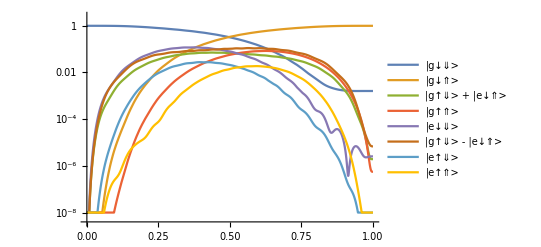

{0.00161131,0.998377,1.94029×10^-6,5.58771×10^-7,2.55202×10^-6,6.83802×10^-6,1.13981×10^-11,2.17452×10^-12}

```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
clearStatus[]:=showStatus[""];
clearStatus[]

clearVariables[]
setVariables[]

ΔE = 0;
Bac = 0;
Eac = 0;

γn = 0;

Clear[B0];
B0sol = NSolve[H[[3]][[3]] == H[[6]][[6]], B0][[1]];
B0 = (B0 /. B0sol);

Clear[Bac]
Clear[Eac]

Htrans = transform[H, Λ];
Mtrans = 2*π*Htrans // N // FullSimplify;
Mtrans = transform[Mtrans, IdentityMatrix[8]*E^(ⅈ*Mtrans[[1]][[1]]*t)] // FullSimplify // Chop;

Tmax = 1*10^-7;

δ1 = Mtrans[[2]][[2]];

ϵ = Mtrans[[6]][[6]];
δϵ = Mtrans[[3]][[3]] - ϵ;

Clear[findState];
findState[Eamplitude_?NumericQ, Bratio_?NumericQ, ω2ShiftFactor_?NumericQ] := (
Clear[ω1, ω2, Eac, Bac];

(* SIMPLIFY HAMILTONIAN *)
Hsim = H;

Do[(
Hsim[[p[[1]]]][[p[[2]]]] = 0;
Hsim[[p[[2]]]][[p[[1]]]] = 0;
),
{p, {{1, 2}, {2, 3}, {2, 7}, {3, 4}, {5, 6}, {6, 7}, {7, 8}}}
];

Do[(
Hsim[[p[[1]]]][[p[[2]]]] = Hsim[[p[[1]]]][[p[[2]]]] - (H[[p[[1]]]][[p[[2]]]]/.{Eac->0, Bac->0});
Hsim[[p[[2]]]][[p[[1]]]] = Hsim[[p[[2]]]][[p[[1]]]] - (H[[p[[2]]]][[p[[1]]]]/.{Eac->0, Bac->0});
),
{p, {{1, 5}, {2, 6}, {3, 7}, {4, 8}}}
];

HsimMid = Hsim;

(* SET Eac AND Bac *)

ω1 = ϵ - 2*δϵ;
ω2 = ω1 - δ1 + ω2ShiftFactor*δϵ;

Eamp[t_] := Eamplitude*tanhWindow[t, Tmax/10, Tmax]^2;
Bamp[t_] := Bratio*Eamp[t]*(8.057132424585235*^6)/(6.213371789014474*^10);
Bac = Bamp[t]*Exp[ⅈ*ω1*t]/2;
Eac = Eamp[t]*Exp[ⅈ*ω2*t]/2;

For[i = 1, i ≤ 8, i = i + 1,
For[j = 1, j < i, j = j + 1,
Hsim[[i]][[j]] = Conjugate[Hsim[[j]][[i]]]
]
];

MsimTI = transform[2*π*Hsim, MatrixExp[ⅈ*DiagonalMatrix[{0, (ω1 - ω2)*t, ω1*t, (2*ω1 - ω2)*t, ω2*t, ω1*t, (ω1 + ω2)*t, 2*ω1*t}]]] // FullSimplify // Chop;

Mtrans = MsimTI;
Mtrans = transform[MsimTI, Λ] // N // FullSimplify;
Mtrans = transform[Mtrans, IdentityMatrix[8]*E^(ⅈ*Mtrans[[1]][[1]]*t)] // FullSimplify // Chop;

(* simulate Mtrans *)
Clear[ψ];
ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};
funcs=Array[ψ[#1][t]&,{Length[ψ0]}];
equations=Flatten@Join[Thread[Mtrans.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
state= NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->30, MaxSteps->Infinity, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]];

pT = Abs[state[[2]]]^2 /. t->Tmax;
If[pT > bestSoFar, bestParameters = {Eamplitude, Bratio, ω2ShiftFactor}];

Print[{pT, {Eamplitude, Bratio, ω2ShiftFactor}}];

pT
)

findState[222.4901014437078,1.,-0.14013391259537455]

LogPlot[Evaluate@Table[Max[Abs[state[[i]]]^2, 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGERotated]
Abs[state]^2 /. t->Tmax
```

```mathematica
.
```

$Aborted

$Aborted

{0.100747,0.100195,0.0375364,0.0246863,0.235378,0.339778,0.104713,0.0569679}

```mathematica
Do[
TimeConstrained[(
bestSoFar = 0;
bestParameters = {};
NMaximize[
{
findState[Ea, Br, ω2F],
100 < Ea < 300,
Br == 1,
-.3 < ω2F < .3
},
{Ea, Br, ω2F},
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]},
MaxIterations->10000
]
), 30*60
],
{i, 100000}
]
```

{0.193492,{115.802,1.,0.10259}}

{0.275135,{100.057,1.,0.0206116}}

{0.173723,{138.254,1.,0.110775}}

{0.282433,{100.022,1.,0.012427}}

{0.302602,{100.093,1.,-0.0367468}}

{0.23774,{100.024,1.,-0.118725}}

{0.293311,{100.049,1.,-0.0633964}}

{0.235486,{100.085,1.,-0.120755}}

{0.299298,{100.064,1.,-0.01473}}

{0.283456,{100.107,1.,0.0119196}}

{0.301148,{100.064,1.,-0.0445674}}

{0.291733,{100.093,1.,-0.0665842}}

{0.302319,{100.071,1.,-0.0276936}}

{0.301159,{100.1,1.,-0.0198729}}

{0.302289,{100.091,1.,-0.0260466}}

{0.30228,{100.073,1.,-0.0383938}}

{0.30257,{100.086,1.,-0.0291334}}

{0.302598,{100.108,1.,-0.0381866}}

{0.301277,{100.115,1.,-0.0458}}

{0.302759,{100.094,1.,-0.0333}}

{0.302625,{100.078,1.,-0.0318602}}

{0.302449,{100.079,1.,-0.0284135}}

{0.302692,{100.089,1.,-0.0346635}}

{0.302747,{100.105,1.,-0.0361033}}

{0.302852,{100.109,1.,-0.0347398}}

{0.302932,{100.119,1.,-0.034778}}

{0.30287,{100.108,1.,-0.0319748}}

{0.303082,{100.133,1.,-0.0334528}}

{0.303244,{100.153,1.,-0.0335292}}

{0.303222,{100.164,1.,-0.0363324}}

{0.303573,{100.198,1.,-0.0350836}}

{0.303892,{100.237,1.,-0.0352363}}

{0.30385,{100.226,1.,-0.0324331}}

{0.304536,{100.31,1.,-0.0341402}}

{0.305181,{100.389,1.,-0.0344458}}

{0.305119,{100.4,1.,-0.037249}}

{0.306444,{100.552,1.,-0.0364584}}

{0.307715,{100.709,1.,-0.0370695}}

{0.307754,{100.698,1.,-0.0342663}}

{0.308995,{100.847,1.,-0.0327749}}

{0.311637,{101.167,1.,-0.0353986}}

{0.31488,{101.556,1.,-0.035875}}

{0.315996,{101.694,1.,-0.0315804}}

{0.319848,{102.186,1.,-0.0288359}}

{0.326061,{102.896,1.,-0.0319361}}

{0.334636,{103.921,1.,-0.0315166}}

{0.338586,{104.551,1.,-0.0244775}}

{0.348832,{106.048,1.,-0.0187787}}

{0.364211,{107.782,1.,-0.0214595}}

{0.385115,{110.58,1.,-0.0177713}}

{0.391137,{112.707,1.,-0.00503334}}

{0.404734,{117.101,1.,0.00820832}}

{0.431598,{121.633,1.,0.00921579}}

{0.439841,{129.425,1.,0.023213}}

{0.378025,{135.946,1.,0.0491926}}

{0.417089,{116.921,1.,-0.00103029}}

{0.462917,{129.246,1.,0.0139744}}

{0.481131,{135.319,1.,0.0168575}}

{0.418292,{147.822,1.,0.0411008}}

{0.450345,{140.097,1.,0.0305681}}

{0.483824,{145.99,1.,0.0242125}}

{0.487458,{154.273,1.,0.0247123}}

{0.539625,{149.495,1.,0.0110017}}

{0.584737,{154.193,1.,0.00121853}}

{0.539313,{173.148,1.,0.00907328}}

{0.657318,{173.068,1.,-0.0144205}}

{0.738856,{182.465,1.,-0.0339868}}

{0.754145,{163.511,1.,-0.0418416}}

{0.783885,{158.692,1.,-0.067299}}

{0.937248,{186.965,1.,-0.102504}}

{0.947093,{203.35,1.,-0.154366}}

{0.692264,{179.577,1.,-0.187678}}

{0.878267,{181.743,1.,-0.0724096}}

{0.98745,{226.401,1.,-0.159476}}

{0.888208,{260.256,1.,-0.205565}}

{0.711189,{248.008,1.,-0.241432}}

{0.971804,{198.31,1.,-0.114665}}

{0.982809,{221.361,1.,-0.119776}}

{0.972311,{249.452,1.,-0.164587}}

{0.991999,{236.667,1.,-0.152107}}

{0.925321,{241.707,1.,-0.191807}}

{0.997901,{226.447,1.,-0.137784}}

{0.971574,{236.713,1.,-0.130414}}

{0.996021,{228.979,1.,-0.152211}}

{0.999309,{218.76,1.,-0.137888}}

{0.992834,{209.806,1.,-0.130779}}

{0.992246,{216.228,1.,-0.123461}}

{0.99924,{225.791,1.,-0.145023}}

{0.995904,{218.104,1.,-0.145127}}

{0.999593,{224.361,1.,-0.13962}}

{0.998246,{217.33,1.,-0.132484}}

{0.999832,{223.676,1.,-0.141888}}

{0.997895,{229.278,1.,-0.14362}}

{0.999869,{221.389,1.,-0.139321}}

{0.999414,{220.704,1.,-0.14159}}

{0.0618836,{234.442,1.,0.173625}}

{0.389985,{145.313,1.,0.04808}}

{0.70911,{223.426,1.,-0.229066}}

{0.176512,{134.297,1.,-0.248855}}

{0.615137,{159.333,1.,-0.169674}}

{0.6086,{237.446,1.,-0.25472}}

{0.684665,{214.413,1.,-0.227045}}

{0.506519,{278.506,1.,-0.286438}}

{0.701362,{189.126,1.,-0.198865}}

{0.743417,{198.139,1.,-0.200886}}

{0.75891,{190.003,1.,-0.187807}}

{0.771807,{224.302,1.,-0.218008}}

{0.772057,{241.89,1.,-0.22758}}

{0.861117,{208.467,1.,-0.18632}}

{0.907991,{200.987,1.,-0.164947}}

{0.889612,{252.875,1.,-0.20472}}

{0.990396,{211.971,1.,-0.142087}}

{0.954047,{197.012,1.,-0.0993407}}

{0.79551,{160.084,1.,-0.102314}}

{0.94889,{229.677,1.,-0.179119}}

{0.986991,{240.661,1.,-0.156259}}

{0.979417,{222.956,1.,-0.119227}}

{0.997074,{224.636,1.,-0.1342}}

{0.967143,{195.946,1.,-0.120028}}

{0.997839,{229.482,1.,-0.147201}}

{0.972803,{242.147,1.,-0.139314}}

{0.998957,{219.515,1.,-0.141394}}

{0.992457,{224.362,1.,-0.154395}}

{0.999449,{224.567,1.,-0.139249}}

{0.997245,{214.6,1.,-0.133442}}

{0.999433,{225.762,1.,-0.143761}}

{0.995938,{230.814,1.,-0.141616}}

{0.999826,{222.34,1.,-0.14145}}

{0.999642,{221.146,1.,-0.136937}}

{0.999227,{218.918,1.,-0.139138}}

{0.999807,{223.155,1.,-0.139221}}

{0.999573,{224.35,1.,-0.143734}}

{0.999857,{221.947,1.,-0.138636}}

{0.999694,{221.131,1.,-0.140865}}

{0.999901,{222.649,1.,-0.139632}}

{0.999476,{222.256,1.,-0.136819}}

{0.999914,{222.319,1.,-0.140292}}

{0.999884,{223.022,1.,-0.141288}}

{0.999913,{222.753,1.,-0.140625}}

{0.999854,{222.423,1.,-0.141285}}

{0.999918,{222.593,1.,-0.140045}}

{0.999914,{222.159,1.,-0.139712}}

{0.999918,{222.307,1.,-0.13994}}

{0.999907,{222.581,1.,-0.139694}}

{0.999919,{222.384,1.,-0.140142}}

{0.999911,{222.099,1.,-0.140037}}

{0.999919,{222.469,1.,-0.140043}}

{0.999919,{222.546,1.,-0.140245}}

{0.999918,{222.631,1.,-0.140146}}

{0.999919,{222.446,1.,-0.140143}}

{0.999919,{222.369,1.,-0.139941}}

{0.999919,{222.502,1.,-0.140169}}

{0.999919,{222.479,1.,-0.140269}}

{0.999919,{222.472,1.,-0.1401}}

{0.999919,{222.528,1.,-0.140126}}

{0.999919,{222.507,1.,-0.14013}}

{0.999919,{222.477,1.,-0.140061}}

{0.999919,{222.496,1.,-0.140142}}

{0.999919,{222.531,1.,-0.140172}}

{0.999919,{222.487,1.,-0.140118}}

{0.999919,{222.475,1.,-0.14013}}

{0.999919,{222.483,1.,-0.14013}}

{0.999919,{222.492,1.,-0.140154}}

{0.999919,{222.488,1.,-0.140127}}

{0.999919,{222.475,1.,-0.140115}}

{0.999919,{222.491,1.,-0.140135}}

{0.999919,{222.495,1.,-0.140132}}

{0.999919,{222.486,1.,-0.14013}}

{0.999919,{222.484,1.,-0.140122}}

{0.999919,{222.489,1.,-0.140132}}

{0.999919,{222.487,1.,-0.140136}}

{0.999919,{222.488,1.,-0.140129}}

{0.999919,{222.49,1.,-0.140131}}

{0.999919,{222.487,1.,-0.140131}}

{0.999919,{222.488,1.,-0.140133}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.486,1.,-0.140129}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.489,1.,-0.140131}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.489,1.,-0.140131}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.488,1.,-0.14013}}

{0.236709,{109.357,1.,0.075774}}

{0.187803,{223.068,1.,0.028924}}

{0.719339,{201.944,1.,-0.0405757}}

{0.287404,{100.03,1.,0.00627431}}

{0.956984,{192.616,1.,-0.110075}}

{0.871962,{234.246,1.,-0.203}}

{0.789857,{294.53,1.,-0.156925}}

{0.805387,{285.203,1.,-0.226425}}

{0.753006,{183.289,1.,-0.179575}}

{0.92804,{266.72,1.,-0.162588}}

{0.789596,{174.133,1.,-0.0462381}}

{0.946337,{257.436,1.,-0.181378}}

{0.908973,{183.332,1.,-0.128866}}

{0.9785,{245.873,1.,-0.154157}}

{0.898048,{181.054,1.,-0.0828544}}

{0.989301,{238.34,1.,-0.156747}}

{0.852746,{291.597,1.,-0.200829}}

{0.998336,{217.361,1.,-0.132764}}

{0.991602,{209.829,1.,-0.135354}}

{0.946203,{188.85,1.,-0.11137}}

{0.999139,{225.968,1.,-0.145403}}

{0.993433,{233.5,1.,-0.142813}}

{0.998389,{227.582,1.,-0.140948}}

{0.992204,{236.189,1.,-0.153588}}

{0.999762,{222.068,1.,-0.13797}}

{0.999059,{220.453,1.,-0.142425}}

{0.999713,{222.236,1.,-0.142056}}

{0.99898,{218.336,1.,-0.134622}}

{0.999738,{224.06,1.,-0.142708}}

{0.999525,{223.892,1.,-0.138622}}

{0.999879,{222.65,1.,-0.141197}}

{0.999561,{220.658,1.,-0.136459}}

{0.999889,{223.209,1.,-0.141146}}

{0.999386,{223.791,1.,-0.144373}}

{0.999905,{222.499,1.,-0.139571}}

{0.999855,{223.058,1.,-0.139519}}

{0.999908,{222.752,1.,-0.140778}}

{0.999897,{222.041,1.,-0.139203}}

{0.999914,{222.333,1.,-0.139688}}

{0.999898,{222.587,1.,-0.140895}}

{0.999917,{222.521,1.,-0.139902}}

{0.999867,{222.102,1.,-0.138813}}

{0.999919,{222.59,1.,-0.140286}}

{0.999915,{222.777,1.,-0.1405}}

{0.999918,{222.666,1.,-0.140297}}

{0.999911,{222.735,1.,-0.140682}}

{0.999919,{222.574,1.,-0.140097}}

{0.999919,{222.498,1.,-0.140086}}

{0.999919,{222.414,1.,-0.139981}}

{0.999919,{222.513,1.,-0.140276}}

{0.999919,{222.528,1.,-0.140231}}

{0.999919,{222.437,1.,-0.140031}}

{0.999918,{222.406,1.,-0.139886}}

{0.999919,{222.498,1.,-0.140145}}

{0.999919,{222.559,1.,-0.1402}}

{0.999919,{222.528,1.,-0.140158}}

{0.999919,{222.528,1.,-0.140216}}

{0.999919,{222.505,1.,-0.140119}}

{0.999919,{222.475,1.,-0.140106}}

{0.999919,{222.467,1.,-0.140132}}

{0.999919,{222.477,1.,-0.140129}}

{0.999919,{222.5,1.,-0.140168}}

{0.999919,{222.481,1.,-0.140121}}

{0.999919,{222.502,1.,-0.140137}}

{0.999919,{222.483,1.,-0.140131}}

{0.999919,{222.466,1.,-0.140107}}

{0.999919,{222.49,1.,-0.140135}}

{0.999919,{222.492,1.,-0.140145}}

{0.999919,{222.484,1.,-0.140127}}

{0.999919,{222.491,1.,-0.140132}}

{0.999919,{222.494,1.,-0.140132}}

{0.999919,{222.497,1.,-0.14014}}

{0.999919,{222.487,1.,-0.14013}}

{0.999919,{222.488,1.,-0.140127}}

{0.999919,{222.488,1.,-0.140129}}

{0.999919,{222.485,1.,-0.140127}}

{0.999919,{222.489,1.,-0.140131}}

{0.999919,{222.488,1.,-0.140132}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.49,1.,-0.140132}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.487,1.,-0.140131}}

{0.999919,{222.489,1.,-0.140131}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.489,1.,-0.140131}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.488,1.,-0.14013}}

{0.00735628,{100.065,1.,0.255904}}

{0.00320045,{141.25,1.,0.282674}}

{0.00333982,{139.917,1.,0.287144}}

{0.0061754,{100.054,1.,0.260374}}

{0.0176717,{100.072,1.,0.229133}}

{0.0363499,{100.084,1.,0.200128}}

{0.0400102,{100.095,1.,0.195658}}

{0.0729571,{100.115,1.,0.1633}}

{0.152152,{100.135,1.,0.107524}}

{0.262065,{100.17,1.,0.0333337}}

{0.295125,{100.201,1.,-0.00349457}}

{0.256618,{100.26,1.,-0.105306}}

{0.218994,{100.256,1.,-0.133461}}

{0.297021,{100.221,1.,-0.0592705}}

{0.267154,{100.252,1.,-0.0960987}}

{0.294659,{100.232,1.,-0.0637406}}

{0.292292,{100.19,1.,0.000975554}}

{0.301699,{100.221,1.,-0.0475616}}

{0.258814,{100.241,1.,-0.103338}}

{0.303536,{100.211,1.,-0.0284553}}

{0.301146,{100.212,1.,-0.0167464}}

{0.303453,{100.214,1.,-0.0273774}}

{0.297674,{100.204,1.,-0.00827114}}

{0.30355,{100.217,1.,-0.037739}}

{0.303411,{100.214,1.,-0.0388169}}

{0.303686,{100.214,1.,-0.0302373}}

{0.303372,{100.22,1.,-0.0395209}}

{0.303723,{100.213,1.,-0.0312217}}

{0.302889,{100.21,1.,-0.02372}}

{0.30375,{100.215,1.,-0.0342342}}

{0.303709,{100.215,1.,-0.0352187}}

{0.303749,{100.214,1.,-0.0339733}}

{0.303612,{100.216,1.,-0.0369858}}

{0.303757,{100.214,1.,-0.0326628}}

{0.303764,{100.215,1.,-0.0329237}}

{0.303764,{100.215,1.,-0.0323988}}

{0.30373,{100.214,1.,-0.0313522}}

{0.30376,{100.215,1.,-0.0335137}}

{0.303764,{100.216,1.,-0.0337746}}

{0.303771,{100.216,1.,-0.0331846}}

{0.303775,{100.216,1.,-0.03302}}

{0.303763,{100.215,1.,-0.032169}}

{0.303768,{100.216,1.,-0.0333732}}

{0.303778,{100.217,1.,-0.0334696}}

{0.303783,{100.218,1.,-0.0337425}}

{0.303792,{100.219,1.,-0.0333893}}

{0.303803,{100.22,1.,-0.0333973}}

{0.303806,{100.222,1.,-0.0341198}}

{0.303812,{100.224,1.,-0.0346698}}

{0.30384,{100.226,1.,-0.0343245}}

{0.303866,{100.231,1.,-0.0346156}}

{0.303844,{100.235,1.,-0.035888}}

{0.303899,{100.241,1.,-0.0358338}}

{0.303932,{100.25,1.,-0.0364158}}

{0.303967,{100.245,1.,-0.0351434}}

{0.304024,{100.25,1.,-0.0347711}}

{0.304086,{100.27,1.,-0.0365714}}

{0.304168,{100.289,1.,-0.0375493}}

{0.304296,{100.29,1.,-0.0359045}}

{0.304476,{100.31,1.,-0.0356489}}

{0.304575,{100.348,1.,-0.038427}}

{0.304755,{100.397,1.,-0.040255}}

{0.305163,{100.418,1.,-0.0383546}}

{0.305656,{100.482,1.,-0.0387573}}

{0.305666,{100.569,1.,-0.0433634}}

{0.305839,{100.699,1.,-0.0472207}}

{0.306951,{100.784,1.,-0.045723}}

{0.307847,{100.977,1.,-0.0484569}}

{0.306478,{101.195,1.,-0.0569204}}

{0.308281,{101.473,1.,-0.0581566}}

{0.308676,{101.86,1.,-0.0636246}}

{0.311106,{101.642,1.,-0.0551611}}

{0.313401,{101.866,1.,-0.0542815}}

{0.312625,{102.749,1.,-0.0694491}}

{0.318396,{102.755,1.,-0.0601061}}

{0.323183,{103.203,1.,-0.0583469}}

{0.320571,{102.321,1.,-0.0431793}}

{0.331214,{103.657,1.,-0.0472446}}

{0.339699,{104.553,1.,-0.0437262}}

{0.342577,{105.435,1.,-0.0588938}}

{0.352059,{106.993,1.,-0.0667511}}

{0.371213,{108.343,1.,-0.0521304}}

{0.395042,{110.913,1.,-0.0490221}}

{0.406743,{113.353,1.,-0.072047}}

{0.435078,{117.752,1.,-0.0862074}}

{0.487345,{121.672,1.,-0.0684785}}

{0.555298,{129.012,1.,-0.0693421}}

{0.580241,{135.851,1.,-0.106527}}

{0.632983,{148.321,1.,-0.13528}}

{0.76912,{159.581,1.,-0.118415}}

{0.882941,{180.495,1.,-0.134519}}

{0.754458,{199.803,1.,-0.200457}}

{0.880823,{231.977,1.,-0.199695}}

{0.995641,{212.669,1.,-0.133757}}

{0.938721,{219.101,1.,-0.100407}}

{0.79893,{161.186,1.,-0.0685806}}

{0.0832864,{237.023,1.,0.242014}}

{0.409959,{153.242,1.,-0.209504}}

{0.314151,{101.484,1.,-0.0379067}}

{0.0443897,{100.089,1.,-0.270316}}

{0.247487,{182.193,1.,0.0591545}}

{0.0455412,{100.096,1.,-0.26885}}

{0.698075,{154.778,1.,-0.0322754}}

{0.771389,{206.537,1.,-0.203872}}

{0.47399,{259.063,1.,-0.286855}}

{0.606499,{208.072,1.,-0.026644}}

{0.885001,{194.365,1.,-0.072359}}

{0.692999,{246.123,1.,-0.243956}}

{0.890857,{177.614,1.,-0.0851955}}

{0.370443,{165.443,1.,0.0463179}}

{0.947392,{196.263,1.,-0.141325}}

{0.824316,{179.513,1.,-0.154161}}

{0.935033,{190.652,1.,-0.0928096}}

{0.976175,{209.301,1.,-0.148939}}

{0.935333,{225.144,1.,-0.180811}}

{0.838402,{214.912,1.,-0.197454}}

{0.969231,{196.717,1.,-0.118971}}

{0.992364,{209.754,1.,-0.126585}}

{0.986885,{216.5,1.,-0.119215}}

{0.987764,{222.338,1.,-0.156553}}

{0.998191,{222.792,1.,-0.134199}}

{0.981472,{229.537,1.,-0.126829}}

{0.964211,{210.208,1.,-0.104231}}

{0.997951,{219.305,1.,-0.143472}}

{0.99558,{232.343,1.,-0.151086}}

{0.999097,{226.696,1.,-0.144961}}

{0.992416,{230.182,1.,-0.135687}}

{0.99977,{222.025,1.,-0.141526}}

{0.995423,{225.929,1.,-0.152288}}

{0.999636,{223.576,1.,-0.138721}}

{0.999205,{218.905,1.,-0.135286}}

{0.999752,{220.852,1.,-0.137705}}

{0.999109,{219.301,1.,-0.14051}}

{0.999876,{222.507,1.,-0.139168}}

{0.999696,{223.679,1.,-0.142989}}

{0.999878,{221.559,1.,-0.139026}}

{0.999476,{222.042,1.,-0.136668}}

{0.999897,{222.029,1.,-0.140312}}

{0.999776,{221.081,1.,-0.140169}}

{0.999906,{222.151,1.,-0.139419}}

{0.999909,{222.62,1.,-0.140704}}

{0.999866,{223.151,1.,-0.141543}}

{0.999905,{222.742,1.,-0.139811}}

{0.999916,{222.564,1.,-0.139936}}

{0.999888,{223.033,1.,-0.141222}}

{0.999918,{222.371,1.,-0.139869}}

{0.999882,{222.315,1.,-0.139101}}

{0.999919,{222.544,1.,-0.140304}}

{0.999917,{222.351,1.,-0.140237}}

{0.999919,{222.405,1.,-0.140162}}

{0.999912,{222.577,1.,-0.140596}}

{0.999919,{222.423,1.,-0.140051}}

{0.999918,{222.283,1.,-0.139909}}

{0.999919,{222.479,1.,-0.140205}}

{0.999919,{222.497,1.,-0.140094}}

{0.999919,{222.543,1.,-0.140061}}

{0.999918,{222.441,1.,-0.13994}}

{0.999919,{222.469,1.,-0.140139}}

{0.999919,{222.544,1.,-0.140182}}

{0.999919,{222.513,1.,-0.140149}}

{0.999919,{222.486,1.,-0.140194}}

{0.999919,{222.494,1.,-0.140119}}

{0.999919,{222.538,1.,-0.14013}}

{0.999919,{222.487,1.,-0.140136}}

{0.999919,{222.467,1.,-0.140106}}

{0.999919,{222.479,1.,-0.140117}}

{0.999919,{222.471,1.,-0.140134}}

{0.999919,{222.488,1.,-0.140123}}

{0.999919,{222.496,1.,-0.140142}}

{0.999919,{222.492,1.,-0.140136}}

{0.999919,{222.49,1.,-0.14015}}

{0.999919,{222.489,1.,-0.14013}}

{0.999919,{222.494,1.,-0.140129}}

{0.999919,{222.488,1.,-0.140135}}

{0.999919,{222.485,1.,-0.140128}}

{0.999919,{222.486,1.,-0.140123}}

{0.999919,{222.488,1.,-0.140132}}

{0.999919,{222.491,1.,-0.140133}}

{0.999919,{222.487,1.,-0.140129}}

{0.999919,{222.486,1.,-0.140132}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.487,1.,-0.140128}}

{0.0381173,{299.949,1.,0.0536844}}

{0.697048,{149.376,1.,-0.0433686}}

{0.0717046,{100.071,1.,-0.240206}}

{0.0438272,{100.023,1.,-0.270902}}

{0.167123,{112.373,1.,-0.206345}}

{0.636375,{161.678,1.,-0.0095075}}

{0.000135833,{198.681,1.,0.153469}}

{0.543638,{133.95,1.,-0.116391}}

{0.248653,{177.104,1.,0.0635152}}

{0.690747,{144.739,1.,-0.0714147}}

{0.549732,{132.437,1.,-0.105276}}

{0.699557,{154.368,1.,-0.0334496}}

{0.617136,{159.005,1.,-0.00540348}}

{0.707068,{148.305,1.,-0.0549119}}

{0.720944,{153.297,1.,-0.0449929}}

{0.732169,{155.258,1.,-0.045805}}

{0.723115,{149.195,1.,-0.0672673}}

{0.758259,{156.147,1.,-0.0581604}}

{0.781004,{160.068,1.,-0.0597847}}

{0.749973,{166.131,1.,-0.0383224}}

{0.803281,{170.941,1.,-0.0523021}}

{0.825933,{178.783,1.,-0.0555506}}

{0.862228,{172.72,1.,-0.0770129}}

{0.893066,{176.015,1.,-0.0963582}}

{0.9389,{194.73,1.,-0.0921241}}

{0.971313,{212.061,1.,-0.108294}}

{0.975892,{209.294,1.,-0.149101}}

{0.87776,{224.549,1.,-0.195877}}

{0.979685,{245.339,1.,-0.161037}}

{0.889667,{280.002,1.,-0.193376}}

{0.891072,{242.572,1.,-0.201845}}

{0.997864,{219.689,1.,-0.131682}}

{0.93728,{255.735,1.,-0.143617}}

{0.99631,{220.904,1.,-0.14773}}

{0.965443,{195.253,1.,-0.118375}}

{0.995469,{232.818,1.,-0.150371}}

{0.990316,{207.775,1.,-0.12904}}

{0.999116,{226.557,1.,-0.145039}}

{0.991379,{225.342,1.,-0.12899}}

{0.999423,{222.013,1.,-0.143045}}

{0.99256,{228.882,1.,-0.156402}}

{0.999752,{221.987,1.,-0.137862}}

{0.998839,{217.443,1.,-0.135868}}

{0.999724,{224.279,1.,-0.142746}}

{0.999075,{224.252,1.,-0.137563}}

{0.999821,{222.573,1.,-0.141675}}

{0.999605,{220.282,1.,-0.13679}}

{0.999883,{223.279,1.,-0.141257}}

{0.999175,{223.866,1.,-0.14507}}

{0.999911,{222.457,1.,-0.139664}}

{0.999809,{223.163,1.,-0.139246}}

{0.999892,{222.721,1.,-0.141068}}

{0.999903,{221.898,1.,-0.139474}}

{0.999804,{221.634,1.,-0.13807}}

{0.999917,{222.449,1.,-0.140318}}

{0.999908,{223.008,1.,-0.140508}}

{0.999917,{222.73,1.,-0.140249}}

{0.999902,{222.723,1.,-0.140904}}

{0.999918,{222.523,1.,-0.139974}}

{0.999916,{222.242,1.,-0.140043}}

{0.999919,{222.608,1.,-0.140198}}

{0.99991,{222.682,1.,-0.139853}}

{0.999919,{222.507,1.,-0.140202}}

{0.999917,{222.592,1.,-0.140426}}

{0.999919,{222.54,1.,-0.140087}}

{0.999919,{222.44,1.,-0.140091}}

{0.999919,{222.355,1.,-0.140038}}

{0.999918,{222.406,1.,-0.140206}}

{0.999919,{222.507,1.,-0.140117}}

{0.999919,{222.439,1.,-0.140006}}

{0.999919,{222.49,1.,-0.140153}}

{0.999919,{222.558,1.,-0.140179}}

{0.999919,{222.469,1.,-0.140113}}

{0.999919,{222.452,1.,-0.140149}}

{0.999919,{222.493,1.,-0.140125}}

{0.999919,{222.472,1.,-0.140085}}

{0.999919,{222.486,1.,-0.140136}}

{0.999919,{222.51,1.,-0.140148}}

{0.999919,{222.479,1.,-0.140122}}

{0.999919,{222.486,1.,-0.140136}}

{0.999919,{222.486,1.,-0.140136}}

{0.999919,{222.486,1.,-0.140136}}

«6 more identical outputs»

{0.0896087,{299.987,1.,-0.0330798}}

{0.0133766,{166.189,1.,0.262816}}

{0.0519063,{205.162,1.,0.260802}}

{0.0974269,{299.935,1.,-0.0350938}}

{0.823575,{299.928,1.,-0.184049}}

{0.628909,{299.927,1.,-0.266138}}

{0.575604,{299.868,1.,-0.27664}}

{0.699626,{299.898,1.,-0.250867}}

{0.796127,{299.9,1.,-0.168778}}

{0.469873,{299.93,1.,-0.10196}}

{0.814473,{299.906,1.,-0.21364}}

{0.779384,{299.935,1.,-0.228911}}

{0.823397,{299.908,1.,-0.183811}}

{0.750004,{299.931,1.,-0.15422}}

{0.829275,{299.912,1.,-0.198785}}

{0.829132,{299.932,1.,-0.199023}}

{0.814251,{299.916,1.,-0.213759}}

{0.829015,{299.925,1.,-0.191476}}

{0.824228,{299.919,1.,-0.206331}}

{0.829763,{299.924,1.,-0.19519}}

{0.829825,{299.904,1.,-0.194953}}

{0.829589,{299.89,1.,-0.192917}}

{0.829007,{299.915,1.,-0.191358}}

{0.829697,{299.913,1.,-0.196928}}

{0.829565,{299.915,1.,-0.193215}}

{0.829786,{299.913,1.,-0.196}}

{0.829866,{299.893,1.,-0.195762}}

{0.829905,{299.878,1.,-0.196048}}

{0.82995,{299.869,1.,-0.195001}}

{0.829998,{299.846,1.,-0.194501}}

{0.830122,{299.821,1.,-0.195597}}

{0.830253,{299.779,1.,-0.195919}}

{0.830337,{299.747,1.,-0.194373}}

{0.830463,{299.681,1.,-0.193535}}

{0.830837,{299.614,1.,-0.194953}}

{0.831244,{299.498,1.,-0.195178}}

{0.831329,{299.4,1.,-0.192794}}

{0.83157,{299.211,1.,-0.191231}}

{0.832685,{299.028,1.,-0.192874}}

{0.833792,{298.701,1.,-0.192544}}

{0.83335,{298.414,1.,-0.188597}}

{0.8359,{297.904,1.,-0.18991}}

{0.838048,{297.25,1.,-0.18925}}

{0.837996,{297.537,1.,-0.193197}}

{0.842542,{296.086,1.,-0.189902}}

{0.846842,{294.779,1.,-0.188582}}

{0.845849,{294.492,1.,-0.184634}}

{0.854775,{292.021,1.,-0.183966}}

{0.862814,{289.407,1.,-0.181324}}

{0.86385,{289.694,1.,-0.185272}}

{0.872168,{287.295,1.,-0.18559}}

{0.88798,{281.922,1.,-0.178333}}

{0.907073,{275.494,1.,-0.173209}}

{0.915094,{273.382,1.,-0.177475}}

{0.936703,{265.369,1.,-0.175551}}

{0.964825,{253.568,1.,-0.163169}}

{0.99197,{236.705,1.,-0.151959}}

{0.993847,{226.58,1.,-0.1543}}

{0.962405,{202.124,1.,-0.144846}}

{0.967396,{197.916,1.,-0.130709}}

{0.994576,{214.78,1.,-0.141919}}

{0.971159,{204.655,1.,-0.144261}}

{0.997227,{228.692,1.,-0.150034}}

{0.998409,{216.892,1.,-0.137653}}

{0.994946,{212.047,1.,-0.12933}}

{0.997104,{230.805,1.,-0.145768}}

{0.999091,{226.798,1.,-0.144806}}

{0.997393,{214.998,1.,-0.132425}}

{0.999222,{218.421,1.,-0.136827}}

{0.99851,{228.328,1.,-0.14398}}

{0.999555,{225.469,1.,-0.142398}}

{0.9986,{217.092,1.,-0.13442}}

{0.999758,{224.372,1.,-0.142209}}

{0.996711,{231.419,1.,-0.147781}}

{0.999891,{221.671,1.,-0.139566}}

{0.999739,{220.574,1.,-0.139377}}

{0.999886,{221.797,1.,-0.140132}}

{0.999435,{219.096,1.,-0.137488}}

{0.999897,{223.053,1.,-0.141029}}

{0.999912,{222.926,1.,-0.140463}}

{0.999874,{223.491,1.,-0.140628}}

{0.999778,{224.308,1.,-0.141926}}

{0.999917,{222.33,1.,-0.140156}}

{0.999912,{222.204,1.,-0.139589}}

{0.0986473,{247.506,1.,0.188711}}

{0.54276,{131.781,1.,-0.0167009}}

{0.0958143,{253.756,1.,0.164981}}

{0.458973,{125.531,1.,0.0070293}}

{0.122643,{100.058,1.,-0.198383}}

{0.383321,{114.357,1.,-0.101609}}

{0.227276,{142.955,1.,0.0919376}}

{0.490488,{121.506,1.,-0.0532225}}

{0.539184,{127.756,1.,-0.0769528}}

{0.62025,{138.031,1.,-0.0404312}}

{0.662452,{146.293,1.,-0.0340355}}

{0.48014,{150.317,1.,0.0262163}}

{0.593423,{133.396,1.,-0.0511605}}

{0.71434,{147.909,1.,-0.0684951}}

{0.77123,{155.973,1.,-0.0943922}}

{0.846602,{168.869,1.,-0.0772672}}

{0.923336,{186.605,1.,-0.0903205}}

{0.927633,{196.285,1.,-0.150677}}

{0.807024,{221.282,1.,-0.208998}}

{0.998722,{226.918,1.,-0.146606}}

{0.944466,{262.391,1.,-0.172712}}

{0.859839,{236.598,1.,-0.206962}}

{0.974795,{199.104,1.,-0.119481}}

{0.955198,{229.736,1.,-0.115409}}

{0.989702,{221.374,1.,-0.124226}}

{0.969286,{249.188,1.,-0.151351}}

{0.994128,{211.625,1.,-0.127448}}

{0.990167,{217.169,1.,-0.149828}}

{0.997151,{218.22,1.,-0.143427}}

{0.986411,{233.514,1.,-0.162584}}

{0.998678,{217.097,1.,-0.136232}}

{0.998961,{225.795,1.,-0.139411}}

{0.99468,{229.582,1.,-0.137402}}

{0.993111,{235.616,1.,-0.149784}}

{0.999895,{221.727,1.,-0.13962}}

{0.998045,{220.603,1.,-0.132425}}

{0.999566,{225.339,1.,-0.14306}}

{0.9991,{221.271,1.,-0.14327}}

{0.999693,{222.402,1.,-0.142305}}

{0.999215,{218.79,1.,-0.138865}}

{0.999821,{223.702,1.,-0.142012}}

{0.999839,{223.026,1.,-0.139327}}

{0.999645,{221.051,1.,-0.136935}}

{0.999906,{223.039,1.,-0.140743}}

{0.999795,{221.74,1.,-0.141036}}

{0.999904,{222.705,1.,-0.139754}}

{0.999813,{224.017,1.,-0.140876}}

{0.999918,{222.299,1.,-0.139934}}

{0.999898,{222.634,1.,-0.140923}}

{0.999915,{222.687,1.,-0.140046}}

{0.999898,{221.947,1.,-0.139238}}

{0.999916,{222.766,1.,-0.140366}}

{0.999917,{222.379,1.,-0.140254}}

{0.999905,{221.912,1.,-0.139822}}

{0.999919,{222.553,1.,-0.14023}}

{0.999918,{222.473,1.,-0.13991}}

{0.999919,{222.45,1.,-0.139996}}

{0.999918,{222.703,1.,-0.140292}}

{0.999919,{222.4,1.,-0.140024}}

{0.999919,{222.503,1.,-0.140258}}

{0.999919,{222.463,1.,-0.140062}}

{0.999919,{222.615,1.,-0.140268}}

{0.999919,{222.454,1.,-0.140085}}

{0.999918,{222.365,1.,-0.139916}}

{0.999919,{222.506,1.,-0.140152}}

{0.999919,{222.497,1.,-0.140175}}

{0.999919,{222.488,1.,-0.140147}}

{0.999919,{222.54,1.,-0.140214}}

{0.999919,{222.475,1.,-0.140117}}

{0.999919,{222.458,1.,-0.140112}}

{0.999919,{222.494,1.,-0.140142}}

{0.999919,{222.481,1.,-0.140112}}

{0.999919,{222.483,1.,-0.140121}}

{0.999919,{222.501,1.,-0.140146}}

{0.999919,{222.482,1.,-0.140124}}

{0.999919,{222.471,1.,-0.140103}}

{0.999919,{222.488,1.,-0.140132}}

{0.999919,{222.487,1.,-0.140136}}

{0.999919,{222.488,1.,-0.140132}}

{0.999919,{222.488,1.,-0.140132}}

{0.999919,{222.488,1.,-0.140132}}

«4 more identical outputs»

{0.0253213,{157.751,1.,0.165023}}

{0.213083,{209.559,1.,0.038518}}

{0.485366,{186.933,1.,-0.238817}}

{0.604255,{238.742,1.,-0.256104}}

{0.654153,{279.237,1.,-0.259891}}

{0.51473,{256.612,1.,-0.278886}}

{0.451466,{299.915,1.,-0.29996}}

{0.58061,{227.429,1.,-0.254103}}

{0.749395,{250.054,1.,-0.235107}}

{0.850136,{246.776,1.,-0.213218}}

{0.807068,{298.584,1.,-0.219006}}

{0.935191,{266.123,1.,-0.172333}}

{0.876568,{259.566,1.,-0.128555}}

{0.951011,{214.315,1.,-0.166545}}

{0.814822,{172.18,1.,-0.140315}}

{0.969779,{233.661,1.,-0.125661}}

{0.830971,{227.104,1.,-0.0818818}}

{0.912961,{181.853,1.,-0.119873}}

{0.980511,{245.055,1.,-0.159218}}

{0.806319,{264.402,1.,-0.118333}}

{0.993766,{226.836,1.,-0.154492}}

{0.933629,{238.23,1.,-0.18805}}

{0.990507,{234.804,1.,-0.141258}}

{0.998379,{216.585,1.,-0.136532}}

{0.981479,{202.349,1.,-0.125189}}

{0.97304,{208.618,1.,-0.149767}}

{0.998491,{228.257,1.,-0.143385}}

{0.993565,{218.005,1.,-0.125425}}

{0.998418,{224.629,1.,-0.147225}}

{0.991976,{236.301,1.,-0.154078}}

{0.99977,{221.514,1.,-0.140919}}

{0.998416,{225.142,1.,-0.137078}}

{0.999365,{224.757,1.,-0.144689}}

{0.997644,{218.014,1.,-0.142222}}

{0.999491,{225.696,1.,-0.143094}}

{0.999892,{222.453,1.,-0.139324}}

{0.999571,{221.301,1.,-0.136642}}

{0.999161,{218.271,1.,-0.137149}}

{0.999837,{223.84,1.,-0.141608}}

{0.999533,{224.779,1.,-0.140014}}

{0.999897,{222.33,1.,-0.140692}}

{0.999809,{220.943,1.,-0.138409}}

{0.999902,{223.116,1.,-0.140808}}

{0.999787,{222.993,1.,-0.142176}}

{0.999918,{222.588,1.,-0.140037}}

{0.999866,{223.374,1.,-0.140153}}

{0.999914,{222.591,1.,-0.140558}}

{0.999912,{222.063,1.,-0.139787}}

{0.999918,{222.326,1.,-0.140042}}

{0.999908,{222.323,1.,-0.139522}}

{0.999919,{222.524,1.,-0.140299}}

{0.999912,{222.263,1.,-0.140303}}

{0.999919,{222.507,1.,-0.140104}}

{0.999917,{222.704,1.,-0.14036}}

{0.999919,{222.421,1.,-0.140122}}

{0.999918,{222.403,1.,-0.139927}}

{0.999919,{222.494,1.,-0.140206}}

{0.999919,{222.58,1.,-0.140188}}

{0.999919,{222.461,1.,-0.140138}}

{0.999919,{222.473,1.,-0.140036}}

{0.999919,{222.489,1.,-0.140163}}

{0.999919,{222.443,1.,-0.140198}}

{0.999919,{222.491,1.,-0.140127}}

{0.999919,{222.519,1.,-0.140153}}

{0.999919,{222.521,1.,-0.140116}}

{0.999919,{222.497,1.,-0.140152}}

{0.999919,{222.469,1.,-0.140127}}

{0.999919,{222.481,1.,-0.140133}}

{0.999919,{222.475,1.,-0.140109}}

{0.999919,{222.491,1.,-0.140141}}

{0.999919,{222.501,1.,-0.140135}}

{0.999919,{222.486,1.,-0.140134}}

{0.999919,{222.485,1.,-0.14012}}

{0.999919,{222.49,1.,-0.140136}}

{0.999919,{222.485,1.,-0.140142}}

{0.999919,{222.489,1.,-0.140131}}

{0.999919,{222.493,1.,-0.140133}}

{0.999919,{222.491,1.,-0.140133}}

{0.999919,{222.491,1.,-0.140129}}

{0.999919,{222.49,1.,-0.140134}}

{0.999919,{222.489,1.,-0.140131}}

{0.999919,{222.489,1.,-0.140131}}

{0.999919,{222.489,1.,-0.140131}}

«1 more identical outputs»

{0.0347818,{195.918,1.,0.233041}}

{0.3633,{218.376,1.,-0.288178}}

{0.504779,{148.363,1.,-0.174983}}

{0.217572,{170.82,1.,-0.28404}}

{0.345206,{177.095,1.,-0.25781}}

{0.672427,{189.644,1.,-0.205351}}

{0.830685,{195.918,1.,-0.179122}}

{0.528033,{125.906,1.,-0.0659271}}

{0.853016,{173.461,1.,-0.0700655}}

{0.647857,{186.01,1.,-0.0176065}}

{0.950189,{243.474,1.,-0.18326}}

{0.735759,{299.913,1.,-0.241927}}

{0.820114,{221.016,1.,-0.0742039}}

{0.946317,{202.193,1.,-0.152892}}

{0.613472,{272.206,1.,-0.266087}}

{0.972646,{198.147,1.,-0.119071}}

{0.988058,{239.428,1.,-0.149439}}

{0.936887,{258.046,1.,-0.147712}}

{0.923108,{194.101,1.,-0.0852494}}

{0.990571,{231.131,1.,-0.158757}}

{0.911244,{272.412,1.,-0.189125}}

{0.998449,{216.713,1.,-0.136584}}

{0.978673,{208.416,1.,-0.145903}}

{0.996482,{231.675,1.,-0.148555}}

{0.994703,{217.258,1.,-0.126382}}

{0.99898,{220.726,1.,-0.134476}}

{0.986772,{205.764,1.,-0.122505}}

{0.999616,{225.197,1.,-0.142042}}

{0.996692,{229.21,1.,-0.139934}}

{0.999609,{219.837,1.,-0.137422}}

{0.999258,{224.309,1.,-0.144988}}

{0.999784,{223.413,1.,-0.14236}}

{0.998163,{228.773,1.,-0.146981}}

{0.999912,{222.071,1.,-0.139812}}

{0.999578,{220.287,1.,-0.140129}}

{0.999826,{223.97,1.,-0.141564}}

{0.999851,{222.628,1.,-0.139015}}

{0.999694,{220.729,1.,-0.137263}}

{0.999899,{223.16,1.,-0.140489}}

{0.999868,{222.603,1.,-0.141285}}

{0.999908,{222.609,1.,-0.140718}}

{0.99986,{221.521,1.,-0.14004}}

{0.999917,{222.75,1.,-0.140377}}

{0.999908,{222.212,1.,-0.139471}}

{0.999916,{222.51,1.,-0.140406}}

{0.999896,{223.189,1.,-0.140971}}

{0.999918,{222.351,1.,-0.140101}}

{0.999918,{222.591,1.,-0.140072}}

{0.999915,{222.191,1.,-0.139797}}

{0.999919,{222.61,1.,-0.140232}}

{0.999917,{222.37,1.,-0.140261}}

{0.999919,{222.536,1.,-0.140119}}

{0.999915,{222.795,1.,-0.14025}}

{0.999919,{222.462,1.,-0.140139}}

{0.999919,{222.387,1.,-0.140026}}

{0.999919,{222.443,1.,-0.140078}}

{0.999919,{222.369,1.,-0.140097}}

{0.999919,{222.494,1.,-0.140114}}

{0.999919,{222.513,1.,-0.140175}}

{0.999919,{222.545,1.,-0.14015}}

{0.999919,{222.483,1.,-0.140141}}

{0.999919,{222.464,1.,-0.14008}}

{0.999919,{222.501,1.,-0.140151}}

{0.999919,{222.489,1.,-0.140179}}

{0.999919,{222.493,1.,-0.14013}}

{0.999919,{222.511,1.,-0.14014}}

{0.999919,{222.49,1.,-0.140141}}

{0.999919,{222.482,1.,-0.14012}}

{0.999919,{222.485,1.,-0.140109}}

{0.999919,{222.488,1.,-0.140133}}

{0.999919,{222.499,1.,-0.140143}}

{0.999919,{222.486,1.,-0.140126}}

{0.999919,{222.482,1.,-0.140129}}

{0.999919,{222.49,1.,-0.14013}}

{0.999919,{222.492,1.,-0.140137}}

{0.999919,{222.488,1.,-0.140128}}

{0.999919,{222.486,1.,-0.140132}}

{0.999919,{222.489,1.,-0.14013}}

{0.999919,{222.488,1.,-0.140126}}

{0.999919,{222.488,1.,-0.140131}}

{0.999919,{222.49,1.,-0.140133}}

{0.999919,{222.488,1.,-0.14013}}

{0.999919,{222.488,1.,-0.140131}}

{0.629131,{299.983,1.,-0.12856}}

{0.242506,{100.009,1.,0.0480733}}

{0.000764929,{100.058,1.,0.297082}}

{0.667983,{299.934,1.,-0.257961}}

{0.682804,{299.93,1.,-0.254702}}

{0.632896,{299.974,1.,-0.265325}}

{0.671356,{299.921,1.,-0.25723}}

{0.717427,{299.877,1.,-0.246606}}

{0.752872,{299.829,1.,-0.237247}}

{0.761463,{299.838,1.,-0.23472}}

{0.794283,{299.796,1.,-0.223465}}

{0.825187,{299.695,1.,-0.20601}}

{0.822219,{299.577,1.,-0.181663}}

{0.830234,{299.662,1.,-0.192227}}

{0.80004,{299.579,1.,-0.169717}}

{0.811139,{299.561,1.,-0.174772}}

{0.827546,{299.62,1.,-0.186945}}

{0.807766,{299.587,1.,-0.173163}}

{0.830354,{299.668,1.,-0.197798}}

{0.827666,{299.711,1.,-0.20308}}

{0.82992,{299.688,1.,-0.199046}}

{0.829873,{299.642,1.,-0.190979}}

{0.83048,{299.676,1.,-0.197029}}

{0.828092,{299.682,1.,-0.2026}}

{0.830647,{299.667,1.,-0.194821}}

{0.830555,{299.676,1.,-0.194052}}

{0.8301,{299.667,1.,-0.191843}}

{0.830624,{299.674,1.,-0.195733}}

{0.830592,{299.665,1.,-0.196501}}

{0.830636,{299.668,1.,-0.195889}}

{0.830673,{299.661,1.,-0.194977}}

{0.830678,{299.655,1.,-0.194599}}

{0.830559,{299.654,1.,-0.19353}}

{0.830666,{299.665,1.,-0.195299}}

{0.830707,{299.652,1.,-0.195077}}

{0.830735,{299.645,1.,-0.195206}}

{0.830742,{299.635,1.,-0.194505}}

{0.830759,{299.62,1.,-0.194108}}

{0.830843,{299.61,1.,-0.194715}}

{0.830924,{299.587,1.,-0.194773}}

{0.830907,{299.563,1.,-0.193676}}

{0.831098,{299.53,1.,-0.194341}}

{0.831264,{299.485,1.,-0.194458}}

{0.831196,{299.51,1.,-0.195555}}

{0.831557,{299.408,1.,-0.19524}}

{0.831861,{299.318,1.,-0.195473}}

{0.831933,{299.293,1.,-0.194375}}

{0.832262,{299.185,1.,-0.193785}}

{0.832909,{299.018,1.,-0.1948}}

{0.833716,{298.784,1.,-0.194971}}

{0.834091,{298.651,1.,-0.193283}}

{0.835093,{298.318,1.,-0.192188}}

{0.836686,{297.916,1.,-0.193374}}

{0.838883,{297.282,1.,-0.193168}}

{0.840049,{296.816,1.,-0.190385}}

{0.842795,{295.832,1.,-0.188093}}

{0.846939,{294.796,1.,-0.189073}}

{0.852756,{293.035,1.,-0.187516}}

{0.85539,{291.585,1.,-0.18244}}

{0.861613,{288.737,1.,-0.177077}}

{0.87195,{285.94,1.,-0.1765}}

{0.884831,{280.994,1.,-0.170704}}

{0.886106,{276.695,1.,-0.160264}}

{0.891071,{268.525,1.,-0.146638}}

{0.908649,{260.783,1.,-0.140266}}

{0.912962,{246.806,1.,-0.12186}}

{0.873272,{234.337,1.,-0.0977942}}

{0.901693,{269.33,1.,-0.152477}}

{0.928323,{247.61,1.,-0.127699}}

{0.93955,{237.152,1.,-0.118229}}

{0.905058,{214.628,1.,-0.0876123}}

{0.922624,{228.303,1.,-0.103828}}

{0.939164,{218.65,1.,-0.100197}}

{0.959112,{227.498,1.,-0.114597}}

{0.973115,{227.096,1.,-0.119982}}

{0.960719,{245.598,1.,-0.138014}}

{0.929821,{241.664,1.,-0.12052}}

{0.0257134,{181.868,1.,0.133652}}

{0.188803,{100.006,1.,0.0842011}}

{0.617828,{159.802,1.,-0.169971}}

{0.675354,{299.998,1.,-0.256348}}

{0.823575,{299.943,1.,-0.206897}}

{0.68402,{241.608,1.,-0.0710699}}

{0.849023,{256.206,1.,-0.117389}}